# Smooth code for VTI_ISO_EI

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,vn1->2,vn2->2.5,eta1->0.1,eta2->0.12,alfa->4,dz->2}
```

{v01→1.5,v02→2,vn1→2,vn2→2.5,eta1→0.1,eta2→0.12,alfa→4,dz→2}

```mathematica
param1={v01->1.5,v02->2,vn1->2,vn2->2.5,eta1->0,eta2->0,alfa->4,dz->2}
```

{v01→1.5,v02→2,vn1→2,vn2→2.5,eta1→0,eta2→0,alfa→4,dz→2}

```mathematica
param2={v01->1.5,v02->2,vn1->1.5,vn2->2,eta1->0,eta2->0,alfa->4,dz->2}
```

{v01→1.5,v02→2,vn1→1.5,vn2→2,eta1→0,eta2→0,alfa→4,dz→2}

```mathematica
z0=3
```

3

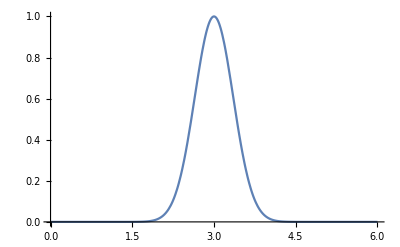

```mathematica
Plot[E^(-alfa*(z-z0)^2)/.param,{z,0,6}]
```

## V0 smoothing

```mathematica
a=v01/.param;
```

```mathematica
b=v02/.param;
```

```mathematica
K=Piecewise[{{a,x<z0},{b,x≥z0}}]/.param
```

Piecewise[{{1.5, x<3}, {2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x<z0
```

```mathematica
m1:=b/;x≥z0
```

```mathematica
F1=(Integrate[K*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

## Vn smoothing

```mathematica
a1=vn1/.param;
```

```mathematica
b1=vn2/.param;
```

```mathematica
K1=Piecewise[{{a1,x<z0},{b1,x≥z0}}];
```

## unsmooth model for V0

```mathematica
m2:=a1/;x<z0;
```

```mathematica
m2:=b1/;x≥z0;
```

```mathematica
Fn1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

## eta smoothing

## composite param

```mathematica
a2=eta1/.param;
```

```mathematica
b2=eta2/.param;
```

```mathematica
K2=Piecewise[{{a2,x<z0},{b2,x≥z0}}]
```

Piecewise[{{0.1, x<3}, {0.12, x≥3}, {0, True}}]

## unsmooth model for m3

```mathematica
m3:=a2/;x<z0;
```

```mathematica
m3:=b2/;x≥z0;
```

```mathematica
Fn1e=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

## convert to the model parameters

```mathematica
V0=F1;
```

```mathematica
Vnmo=Fn1;
```

```mathematica
ETA=Fn1e;
```

## unsmoothed model parameters

```mathematica
vel1:=v01/;z<z0;
```

```mathematica
vel1:=v02/;z≥z0;
```

```mathematica
veln1:=vn1/;z<z0;
```

```mathematica
veln1:=vn2/;z≥z0;
```

```mathematica
ET1:=eta1/;z<z0;
```

```mathematica
ET1:=eta2/;z≥z0;
```

```mathematica
Xp=Sum[(0.001*p Vnmo^2)/(V0 (1-2 ETA p^2 Vnmo^2)^(3/2) √(1-(1+2 ETA) p^2 Vnmo^2)),{z,0,6,0.001}];
```

```mathematica
Tp=Sum[(0.001*((1-2 ETA p^2 Vnmo^2)^2+2ETA*p^4Vnmo^4))/(V0 (1-2 ETA p^2 Vnmo^2)^(3/2) √(1-(1+2 ETA) p^2 Vnmo^2)),{z,0,6,0.001}];
```

```mathematica
Xp0=Sum[(p veln1^2 *0.001)/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param,{z,0,6,0.001}];
```

```mathematica
Tp0=Sum[(0.001*((1-2 ET1 p^2 veln1^2)^2+2ET1*p^4veln1^4))/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param,{z,0,6,0.001}];
```

```mathematica
DTp=Abs[(Tp0-Tp)];
```

```mathematica
å1=DTp/.p->0;
```

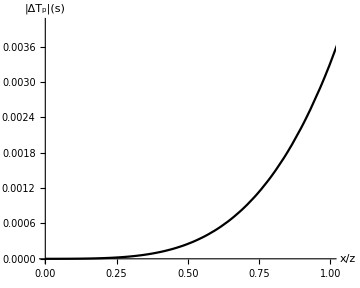

```mathematica
aaa=ParametricPlot[{Xp/6,DTp-å1},{p,0,0.9},PlotRange->{{0,1},{0,0.004}},PlotStyle->Black,AspectRatio->0.8,AxesLabel->{Style["x/z",FontSize->15],Style["|ΔT_p|(s)",FontSize->15]}]
```

## EI case

## V0 smoothing

```mathematica
ai=v01/.param1;
```

```mathematica
bi=v02/.param1;
```

```mathematica
Ki=Piecewise[{{ai,x<z0},{bi,x≥z0}}]/.param1
```

Piecewise[{{1.5, x<3}, {2, x≥3}, {0, True}}]

```mathematica
m1i:=ai/;x<z0
```

```mathematica
m1i:=bi/;x≥z0
```

```mathematica
F1i=(Integrate[Ki*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param1;
```

## Vn smoothing

```mathematica
a1i=vn1/.param1;
```

```mathematica
b1i=vn2/.param1;
```

```mathematica
K1i=Piecewise[{{a1i,x<z0},{b1i,x≥z0}}];
```

## unsmooth model for V0

```mathematica
m2i:=a1i/;x<z0;
```

```mathematica
m2i:=b1i/;x≥z0;
```

```mathematica
Fn1i=(Integrate[K1i*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param1;
```

## eta smoothing

## composite param

```mathematica
a2i=eta1/.param1;
```

```mathematica
b2i=eta2/.param1;
```

```mathematica
K2i=Piecewise[{{a2i,x<z0},{b2i,x≥z0}}]
```

0

## unsmooth model for m3

```mathematica
m3i:=a2i/;x<z0;
```

```mathematica
m3i:=b2i/;x≥z0;
```

```mathematica
Fn1ei=(Integrate[K2i*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param1;
```

## convert to the model parameters

```mathematica
V0i=F1i;
```

```mathematica
Vnmoi=Fn1i;
```

```mathematica
ETAi=Fn1ei;
```

## unsmoothed model parameters

```mathematica
vel1:=v01/;z<z0;
```

```mathematica
vel1:=v02/;z≥z0;
```

```mathematica
veln1:=vn1/;z<z0;
```

```mathematica
veln1:=vn2/;z≥z0;
```

```mathematica
ET1:=eta1/;z<z0;
```

```mathematica
ET1:=eta2/;z≥z0;
```

```mathematica
Xpi=Sum[(0.001*p Vnmoi^2)/(V0i (1-2 ETAi p^2 Vnmoi^2)^(3/2) √(1-(1+2 ETAi) p^2 Vnmoi^2)),{z,0,6,0.001}];
```

```mathematica
Tpi=Sum[(0.001*((1-2 ETAi p^2 Vnmoi^2)^2+2ETAi*p^4Vnmoi^4))/(V0i (1-2 ETAi p^2 Vnmoi^2)^(3/2) √(1-(1+2 ETAi) p^2 Vnmoi^2)),{z,0,6,0.001}];
```

```mathematica
Xp0i=Sum[(p veln1^2 *0.001)/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param1,{z,0,6,0.001}];
```

```mathematica
Tp0i=Sum[(0.001*((1-2 ET1 p^2 veln1^2)^2+2ET1*p^4veln1^4))/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param1,{z,0,6,0.001}];
```

```mathematica
DTpi=Abs[(Tp0i-Tpi)];
```

```mathematica
å2=DTpi/.p->0;
```

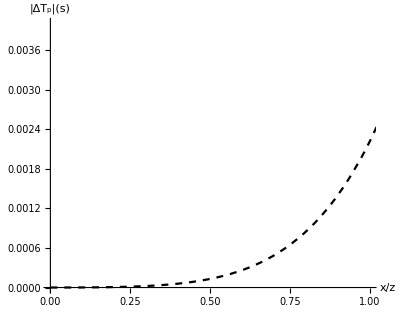

```mathematica
bbb=ParametricPlot[{Xpi/6,DTpi-å2},{p,0,0.9},PlotRange->{{0,1},{0,0.004}},PlotStyle->Directive[Dashed,Black],AspectRatio->0.8,AxesLabel->{Style["x/z",FontSize->15],Style["|ΔT_p|(s)",FontSize->15]}]
```

## ISO case

## V0 smoothing

```mathematica
aj=v01/.param2;
```

```mathematica
bj=v02/.param2;
```

```mathematica
Kj=Piecewise[{{a,x<z0},{b,x≥z0}}]/.param2
```

Piecewise[{{1.5, x<3}, {2, x≥3}, {0, True}}]

```mathematica
m1j:=aj/;x<z0
```

```mathematica
m1j:=bj/;x≥z0
```

```mathematica
F1j=(Integrate[Kj*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param2;
```

## Vn smoothing

```mathematica
a1j=vn1/.param2;
```

```mathematica
b1j=vn2/.param2;
```

```mathematica
K1j=Piecewise[{{a1j,x<z0},{b1j,x≥z0}}];
```

## unsmooth model for V0

```mathematica
m2j:=a1j/;x<z0;
```

```mathematica
m2j:=b1j/;x≥z0;
```

```mathematica
Fn1j=(Integrate[K1j*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param2;
```

## eta smoothing

## composite param

```mathematica
a2j=eta1/.param2;
```

```mathematica
b2j=eta2/.param2;
```

```mathematica
K2j=Piecewise[{{a2j,x<z0},{b2j,x≥z0}}]
```

0

## unsmooth model for m3

```mathematica
m3j:=a2j/;x<z0;
```

```mathematica
m3j:=b2j/;x≥z0;
```

```mathematica
Fn1ej=(Integrate[K2j*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param2;
```

## convert to the model parameters

```mathematica
V0j=F1j;
```

```mathematica
Vnmoj=Fn1j;
```

```mathematica
ETAj=Fn1ej;
```

## unsmoothed model parameters

```mathematica
vel1:=v01/;z<z0;
```

```mathematica
vel1:=v02/;z≥z0;
```

```mathematica
veln1:=vn1/;z<z0;
```

```mathematica
veln1:=vn2/;z≥z0;
```

```mathematica
ET1:=eta1/;z<z0;
```

```mathematica
ET1:=eta2/;z≥z0;
```

```mathematica
Xpj=Sum[(0.001*p Vnmoj^2)/(V0j(1-2 ETAj p^2 Vnmoj^2)^(3/2) √(1-(1+2 ETAj) p^2 Vnmoj^2)),{z,0,6,0.001}];
```

```mathematica
Tpj=Sum[(0.001*((1-2 ETAj p^2 Vnmoj^2)^2+2ETAj*p^4Vnmoj^4))/(V0j (1-2 ETAj p^2 Vnmoj^2)^(3/2) √(1-(1+2 ETAj) p^2 Vnmoj^2)),{z,0,6,0.001}];
```

```mathematica
Xp0j=Sum[(p veln1^2 *0.001)/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param2,{z,0,6,0.001}];
```

```mathematica
Tp0j=Sum[(0.001*((1-2 ET1 p^2 veln1^2)^2+2ET1*p^4veln1^4))/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param2,{z,0,6,0.001}];
```

```mathematica
DTpj=Abs[(Tp0j-Tpj)];
```

```mathematica
å3=DTpj/.p->0;
```

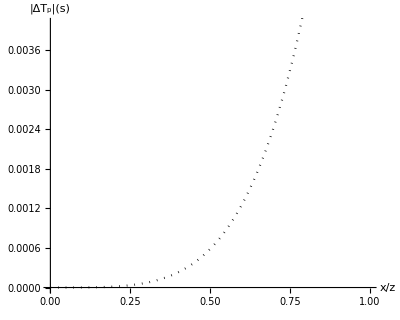

```mathematica
ccc=ParametricPlot[{Xpj/6,DTpj-å3},{p,0,0.9},PlotRange->{{0,1},{0,0.004}},PlotStyle->Directive[Dotted,Black],AspectRatio->0.8,AxesLabel->{Style["x/z",FontSize->15],Style["|ΔT_p|(s)",FontSize->15]}]
```

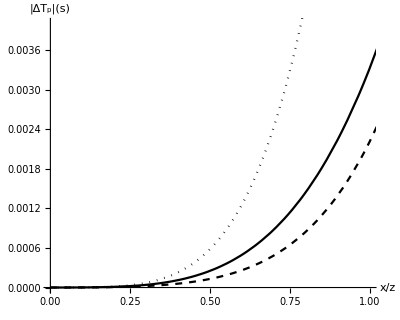

```mathematica
Show[aaa,bbb,ccc]
```

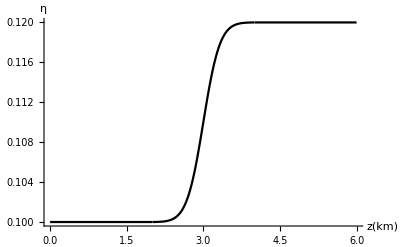

```mathematica
P1=Plot[ETA,{z,0,6},PlotStyle->Directive[Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["η",FontSize->15]}]
```

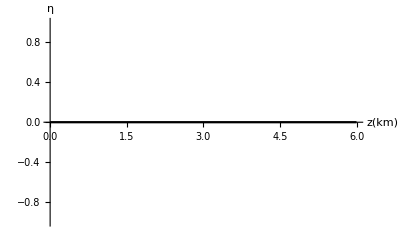

```mathematica
P2=Plot[ETAi,{z,0,6},PlotStyle->Directive[Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["η",FontSize->15]}]
```

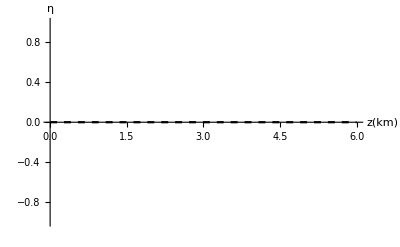

```mathematica
P3=Plot[ETAj,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["η",FontSize->15]}]
```

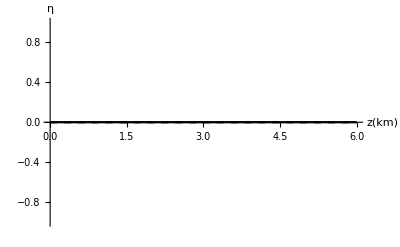

```mathematica
Show[P2,P3]
```